# Entropy in Tweet (and Conversation, Book, Chapter...)

Assume uniform distribution of probabilities.
You want the probability of the word to be low.
You want the language to be uncommon.
Although, you do need a distribution of probabilities of the words.

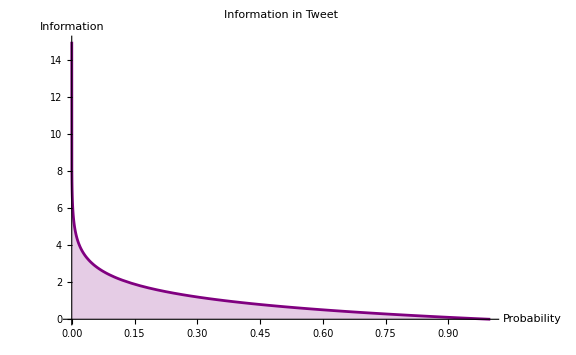

```mathematica
Plot[-Log[p],{p,0,1},
PlotRange->{0,15},
AxesLabel->{Probability, Information},
PlotStyle -> Purple,
Filling -> Axis,
PlotLabel -> "Information in Tweet",
ImageSize->Large]
```

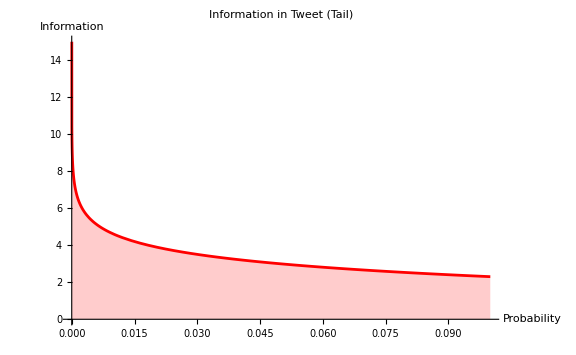

```mathematica
Plot[-Log[p],{p,0,0.1},
PlotRange->{0,15},
AxesLabel->{Probability, Information},
PlotStyle -> Red,
Filling -> Axis,
PlotLabel -> "Information in Tweet (Tail)",
ImageSize->Large]
```

```mathematica
TableForm[Table[{p,-Log[p]},{p,0,1,0.01}],TableHeadings->{None,{"Probability (p)", "Dimensionless entropy (nats)"}}]
```

Probability (p) | Dimensionless entropy (nats)
0. | Indeterminate
0.01 | 4.60517
0.02 | 3.91202
0.03 | 3.50656
0.04 | 3.21888
0.05 | 2.99573
0.06 | 2.81341
0.07 | 2.65926
0.08 | 2.52573
0.09 | 2.40795
0.1 | 2.30259
0.11 | 2.20727
0.12 | 2.12026
0.13 | 2.04022
0.14 | 1.96611
0.15 | 1.89712
0.16 | 1.83258
0.17 | 1.77196
0.18 | 1.7148
0.19 | 1.66073
0.2 | 1.60944
0.21 | 1.56065
0.22 | 1.51413
0.23 | 1.46968
0.24 | 1.42712
0.25 | 1.38629
0.26 | 1.34707
0.27 | 1.30933
0.28 | 1.27297
0.29 | 1.23787
0.3 | 1.20397
0.31 | 1.17118
0.32 | 1.13943
0.33 | 1.10866
0.34 | 1.07881
0.35 | 1.04982
0.36 | 1.02165
0.37 | 0.994252
0.38 | 0.967584
0.39 | 0.941609
0.4 | 0.916291
0.41 | 0.891598
0.42 | 0.867501
0.43 | 0.84397
0.44 | 0.820981
0.45 | 0.798508
0.46 | 0.776529
0.47 | 0.755023
0.48 | 0.733969
0.49 | 0.71335
0.5 | 0.693147
0.51 | 0.673345
0.52 | 0.653926
0.53 | 0.634878
0.54 | 0.616186
0.55 | 0.597837
0.56 | 0.579818
0.57 | 0.562119
0.58 | 0.544727
0.59 | 0.527633
0.6 | 0.510826
0.61 | 0.494296
0.62 | 0.478036
0.63 | 0.462035
0.64 | 0.446287
0.65 | 0.430783
0.66 | 0.415515
0.67 | 0.400478
0.68 | 0.385662
0.69 | 0.371064
0.7 | 0.356675
0.71 | 0.34249
0.72 | 0.328504
0.73 | 0.314711
0.74 | 0.301105
0.75 | 0.287682
0.76 | 0.274437
0.77 | 0.261365
0.78 | 0.248461
0.79 | 0.235722
0.8 | 0.223144
0.81 | 0.210721
0.82 | 0.198451
0.83 | 0.18633
0.84 | 0.174353
0.85 | 0.162519
0.86 | 0.150823
0.87 | 0.139262
0.88 | 0.127833
0.89 | 0.116534
0.9 | 0.105361
0.91 | 0.0943107
0.92 | 0.0833816
0.93 | 0.0725707
0.94 | 0.0618754
0.95 | 0.0512933
0.96 | 0.040822
0.97 | 0.0304592
0.98 | 0.0202027
0.99 | 0.0100503
1. | 0.

```mathematica
TableForm[Table[{p,-Log[p]},{p,0,0.01,0.0001}],TableHeadings->{None,{"Probability (p)", "Dimensionless entropy (nats)"}}]
```

Probability (p) | Dimensionless entropy (nats)
0. | Indeterminate
0.0001 | 9.21034
0.0002 | 8.51719
0.0003 | 8.11173
0.0004 | 7.82405
0.0005 | 7.6009
0.0006 | 7.41858
0.0007 | 7.26443
0.0008 | 7.1309
0.0009 | 7.01312
0.001 | 6.90776
0.0011 | 6.81245
0.0012 | 6.72543
0.0013 | 6.64539
0.0014 | 6.57128
0.0015 | 6.50229
0.0016 | 6.43775
0.0017 | 6.37713
0.0018 | 6.31997
0.0019 | 6.2659
0.002 | 6.21461
0.0021 | 6.16582
0.0022 | 6.1193
0.0023 | 6.07485
0.0024 | 6.03229
0.0025 | 5.99146
0.0026 | 5.95224
0.0027 | 5.9145
0.0028 | 5.87814
0.0029 | 5.84304
0.003 | 5.80914
0.0031 | 5.77635
0.0032 | 5.7446
0.0033 | 5.71383
0.0034 | 5.68398
0.0035 | 5.65499
0.0036 | 5.62682
0.0037 | 5.59942
0.0038 | 5.57275
0.0039 | 5.54678
0.004 | 5.52146
0.0041 | 5.49677
0.0042 | 5.47267
0.0043 | 5.44914
0.0044 | 5.42615
0.0045 | 5.40368
0.0046 | 5.3817
0.0047 | 5.36019
0.0048 | 5.33914
0.0049 | 5.31852
0.005 | 5.29832
0.0051 | 5.27851
0.0052 | 5.2591
0.0053 | 5.24005
0.0054 | 5.22136
0.0055 | 5.20301
0.0056 | 5.18499
0.0057 | 5.16729
0.0058 | 5.1499
0.0059 | 5.1328
0.006 | 5.116
0.0061 | 5.09947
0.0062 | 5.08321
0.0063 | 5.06721
0.0064 | 5.05146
0.0065 | 5.03595
0.0066 | 5.02069
0.0067 | 5.00565
0.0068 | 4.99083
0.0069 | 4.97623
0.007 | 4.96185
0.0071 | 4.94766
0.0072 | 4.93367
0.0073 | 4.91988
0.0074 | 4.90628
0.0075 | 4.89285
0.0076 | 4.87961
0.0077 | 4.86653
0.0078 | 4.85363
0.0079 | 4.84089
0.008 | 4.82831
0.0081 | 4.81589
0.0082 | 4.80362
0.0083 | 4.7915
0.0084 | 4.77952
0.0085 | 4.76769
0.0086 | 4.75599
0.0087 | 4.74443
0.0088 | 4.733
0.0089 | 4.7217
0.009 | 4.71053
0.0091 | 4.69948
0.0092 | 4.68855
0.0093 | 4.67774
0.0094 | 4.66705
0.0095 | 4.65646
0.0096 | 4.64599
0.0097 | 4.63563
0.0098 | 4.62537
0.0099 | 4.61522
0.01 | 4.60517